```mathematica
ClearAll["Global`*"];
```

```mathematica
$Assumptions={ω∈Reals,χ∈Reals,κ∈Reals&&κ≥0,t∈Reals&&t≥0,s∈Reals&&s≥0,Ω∈Reals,x[t]∈Reals,p[t]∈Reals,x'[t]∈Reals,p'[t]∈Reals,ϵ1[t]∈Reals,ϵ2[t]∈Reals,α∈Reals,β∈Reals,ϕ∈Reals,σ∈Reals};
```

Langevin equations

```mathematica
Le[t_,χ_,κ_,σ_]=D[a[t],t]+I*(σ*χ)*a[t]+κ/2*a[t]+Ω[t];
Letime[t_,χ_,κ_,ϵ0_,σ_,ϕ_]=Le[t,χ,κ,σ]/.{Ω[t]->ϵ0 Sin[σ*χ*t+ϕ]+I*ϵ0 Cos[σ*χ*t+ϕ]};
```

```mathematica
Soltime[t_,χ_,κ_,ϵ0_,σ_,ϕ_]=FullSimplify[DSolve[{Letime[t,χ,κ,ϵ0,σ,ϕ]==0,a[0]==0},a[t],t]];
```

```mathematica
tmin[χ_,κ_,ϵ0_,α_,β_,σ_,ϕ_]:=FindRoot[Abs[Soltime[t,χ,κ,ϵ0,σ,ϕ][[1,1,2]]]==Abs[α+I*β],{t,0}]
phisol[χ_,κ_,ϵ0_,α_,β_,σ_]:=FindRoot[Soltime[tmin[χ,κ,ϵ0,α,β,σ,π/2][[1,2]],χ,κ,ϵ0,σ,ϕ][[1,1,2]]==α+I*β,{ϕ,0}]
```

```mathematica
χ=0.25;
κ=2*π*0.01;
n=1;
ϵtem=0.2;
```

minimal time:5.43937

FindRoot::nlnum: The function value {-100+2.98023×10^-7 ⅇ^(-7.45058×10^-9 (0.0628319+Re[Times[«2»]]))} is not a list of numbers with dimensions {1} at {t} = {1.49012×10^-8}.

FindRoot::nlnum: The function value {False} is not a list of numbers with dimensions {1} at {ϕ} = {0.}.

phi:100

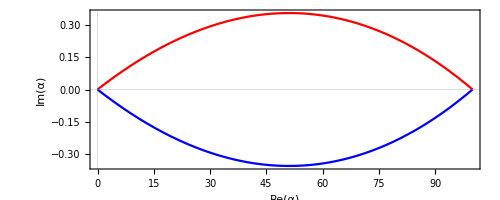

```mathematica
tmin1=tmin[χ,κ,ϵtem,n,0,1,π/2][[1,2]];
Print["minimal time:",tmin1]
θ[σ_]:=Re[phisol[χ,κ,ϵtem,n,0,σ][[1,2]]];
Print["phi:",θ[1]]
ParametricPlot[{{Re[Soltime[t,χ,κ,ϵtem,1,θ[1]][[1,1,2]]],Im[Soltime[t,χ,κ,ϵtem,1,θ[1]][[1,1,2]]]},{Re[Soltime[t,χ,κ,ϵtem,-1,θ[-1]][[1,1,2]]],Im[Soltime[t,χ,κ,ϵtem,-1,θ[-1]][[1,1,2]]]}(*{Re[Soltimeminus[t,χ,κ,ϵtem,ϕ1][[1,1,2]]],Im[Soltimeminus[t,χ,κ,ϵtem,ϕ1][[1,1,2]]]}*)},{t,0,tmin1},PlotStyle->{Red,Blue},PlotTheme->"Scientific",FrameStyle->Directive[Thickness[0.003],Black,20],FrameLabel->{"Re(α)","Im(α)"},LabelStyle->Directive[Black,16,FontFamily->"Times"]]
```

```mathematica
phi={θ[-1],θ[1]};
phi[[(-1+3)/2]]
```

-0.210954

Signal to Noise Ratio

```mathematica
Hd[τ_,χ_,κ_,σ_,α_,ϕ_]=κ*Integrate[Conjugate[Soltime[t,χ,κ,ϵtem,σ,phi[[(σ+3)/2]]][[1,1,2]]]*Exp[I*ϕ]+Soltime[t,χ,κ,ϵtem,σ,phi[[(σ+3)/2]]][[1,1,2]]*Exp[I*ϕ],{t,0,τ}];
```

Part::pkspec1: The expression (3+σ)/2 cannot be used as a part specification.

```mathematica
H2d[τ_,χ_,κ_,σ_,α_,ϕ_]=TrigToExp[κ*τ+κ^2*Integrate[Conjugate[Soltime[t,χ,κ,ϵtem,σ,phi[[(σ+3)/2]]][[1,1,2]]]*Conjugate[Soltime[t,χ,κ,ϵtem,σ,phi[[(σ+3)/2]]][[1,1,2]]]*Exp[2*I*ϕ]+Soltime[t,χ,κ,ϵtem,σ,phi[[(σ+3)/2]]][[1,1,2]]*Soltime[t,χ,κ,ϵtem,σ,phi[[(σ+3)/2]]][[1,1,2]]*Exp[-2*I*ϕ]+2*Conjugate[Soltime[t,χ,κ,ϵtem,σ,phi[[(σ+3)/2]]][[1,1,2]]]*Soltime[t,χ,κ,ϵtem,σ,phi[[(σ+3)/2]]][[1,1,2]],{t,0,τ},{x,0,τ}]];
```

Part::pkspec1: The expression (3+σ)/2 cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

```mathematica
Hdn[τ_,χ_,κ_,α_,ϕ_]=Simplify[H2d[τ,χ,κ,1,α,0]-Hd[τ,χ,κ,-1,α,0]^2];
```

```mathematica
SNR[τ_,χ_,κ_,α_,ϕ_]=Simplify[(Hd[τ,χ,κ,1,α,ϕ]+Hd[τ,χ,κ,-1,α,ϕ])^2/(2*Hdn[τ,χ,κ,α,ϕ])];
```

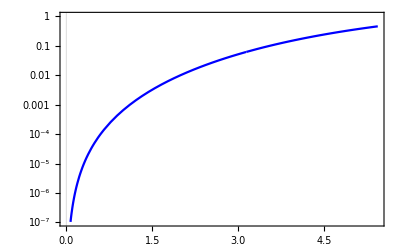

```mathematica
f1=LogPlot[{Re[SNR[t,χ,κ,n,0]]},{t,0,tmin1},LabelStyle->{FontFamily->"Times New Roman",FontSize->18,Black},Frame->True,FrameStyle->{{AbsoluteThickness[2],AbsoluteThickness[2]},{AbsoluteThickness[2],AbsoluteThickness[2]}},PlotTheme->"Scientific",PlotStyle->Blue]
```

```mathematica
χ=0.025;
κ=2*π*0.01;
n=10;
ϵtem=2;
```

```mathematica
tmin1=tmin[χ,κ,ϵtem,n,0,1,π/2][[1,2]];
Print["minimal time:",tmin1]
θ[σ_]:=Re[phisol[χ,κ,ϵtem,n,0,σ][[1,2]]];
Print["phi:",θ[1]]
ParametricPlot[{{Re[Soltime[t,χ,κ,ϵtem,1,θ[1]][[1,1,2]]],Im[Soltime[t,χ,κ,ϵtem,1,θ[1]][[1,1,2]]]},{Re[Soltime[t,χ,κ,ϵtem,-1,θ[-1]][[1,1,2]]],Im[Soltime[t,χ,κ,ϵtem,-1,θ[-1]][[1,1,2]]]}(*{Re[Soltimeminus[t,χ,κ,ϵtem,ϕ1][[1,1,2]]],Im[Soltimeminus[t,χ,κ,ϵtem,ϕ1][[1,1,2]]]}*)},{t,0,tmin1},PlotStyle->{Red,Blue},PlotTheme->"Scientific",FrameStyle->Directive[Thickness[0.003],Black,20],FrameLabel->{"Re(α)","Im(α)"},LabelStyle->Directive[Black,16,FontFamily->"Times"]]
```

minimal time:5.43937

FindRoot::nlnum: The function value {-100+2.98023×10^-7 ⅇ^(-7.45058×10^-9 (0.0628319+Re[Times[«2»]]))} is not a list of numbers with dimensions {1} at {t} = {1.49012×10^-8}.

FindRoot::nlnum: The function value {False} is not a list of numbers with dimensions {1} at {ϕ} = {0.}.

phi:100

-Graphics-

```mathematica
phi={θ[-1],θ[1]};
phi[[(-1+3)/2]]
```

-0.210954

Signal to Noise Ratio

```mathematica
Hd[τ_,χ_,κ_,σ_,α_,ϕ_]=κ*Integrate[Conjugate[Soltime[t,χ,κ,ϵtem,σ,phi[[(σ+3)/2]]][[1,1,2]]]*Exp[I*ϕ]+Soltime[t,χ,κ,ϵtem,σ,phi[[(σ+3)/2]]][[1,1,2]]*Exp[I*ϕ],{t,0,τ}];
```

Part::pkspec1: The expression (3+σ)/2 cannot be used as a part specification.

```mathematica
H2d[τ_,χ_,κ_,σ_,α_,ϕ_]=TrigToExp[κ*τ+κ^2*Integrate[Conjugate[Soltime[t,χ,κ,ϵtem,σ,phi[[(σ+3)/2]]][[1,1,2]]]*Conjugate[Soltime[t,χ,κ,ϵtem,σ,phi[[(σ+3)/2]]][[1,1,2]]]*Exp[2*I*ϕ]+Soltime[t,χ,κ,ϵtem,σ,phi[[(σ+3)/2]]][[1,1,2]]*Soltime[t,χ,κ,ϵtem,σ,phi[[(σ+3)/2]]][[1,1,2]]*Exp[-2*I*ϕ]+2*Conjugate[Soltime[t,χ,κ,ϵtem,σ,phi[[(σ+3)/2]]][[1,1,2]]]*Soltime[t,χ,κ,ϵtem,σ,phi[[(σ+3)/2]]][[1,1,2]],{t,0,τ},{x,0,τ}]];
```

Part::pkspec1: The expression (3+σ)/2 cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

```mathematica
Hdn[τ_,χ_,κ_,α_,ϕ_]=Simplify[H2d[τ,χ,κ,1,α,0]-Hd[τ,χ,κ,-1,α,0]^2];
```

```mathematica
SNR[τ_,χ_,κ_,α_,ϕ_]=Simplify[(Hd[τ,χ,κ,1,α,ϕ]+Hd[τ,χ,κ,-1,α,ϕ])^2/(2*Hdn[τ,χ,κ,α,ϕ])];
```

```mathematica
f2=LogPlot[{Re[SNR[t,χ,κ,n,0]]},{t,0,tmin1},LabelStyle->{FontFamily->"Times New Roman",FontSize->18,Black},Frame->True,FrameStyle->{{AbsoluteThickness[2],AbsoluteThickness[2]},{AbsoluteThickness[2],AbsoluteThickness[2]}},PlotTheme->"Scientific",PlotStyle->Green]
```

-Graphics-

```mathematica
χ=0.0025;
κ=2*π*0.01;
n=100;
ϵtem=20;
```

```mathematica
tmin1=tmin[χ,κ,ϵtem,n,0,1,π/2][[1,2]];
Print["minimal time:",tmin1]
θ[σ_]:=Re[phisol[χ,κ,ϵtem,n,0,σ][[1,2]]];
Print["phi:",θ[1]]
ParametricPlot[{{Re[Soltime[t,χ,κ,ϵtem,1,θ[1]][[1,1,2]]],Im[Soltime[t,χ,κ,ϵtem,1,θ[1]][[1,1,2]]]},{Re[Soltime[t,χ,κ,ϵtem,-1,θ[-1]][[1,1,2]]],Im[Soltime[t,χ,κ,ϵtem,-1,θ[-1]][[1,1,2]]]}(*{Re[Soltimeminus[t,χ,κ,ϵtem,ϕ1][[1,1,2]]],Im[Soltimeminus[t,χ,κ,ϵtem,ϕ1][[1,1,2]]]}*)},{t,0,tmin1},PlotStyle->{Red,Blue},PlotTheme->"Scientific",FrameStyle->Directive[Thickness[0.003],Black,20],FrameLabel->{"Re(α)","Im(α)"},LabelStyle->Directive[Black,16,FontFamily->"Times"]]
```

minimal time:5.43937

FindRoot::nlnum: The function value {-100+2.98023×10^-7 ⅇ^(-7.45058×10^-9 (0.0628319+Re[Times[«2»]]))} is not a list of numbers with dimensions {1} at {t} = {1.49012×10^-8}.

FindRoot::nlnum: The function value {False} is not a list of numbers with dimensions {1} at {ϕ} = {0.}.

phi:100

-Graphics-

```mathematica
phi={θ[-1],θ[1]};
phi[[(-1+3)/2]]
```

-0.210954

Signal to Noise Ratio

```mathematica
Hd[τ_,χ_,κ_,σ_,α_,ϕ_]=κ*Integrate[Conjugate[Soltime[t,χ,κ,ϵtem,σ,phi[[(σ+3)/2]]][[1,1,2]]]*Exp[I*ϕ]+Soltime[t,χ,κ,ϵtem,σ,phi[[(σ+3)/2]]][[1,1,2]]*Exp[I*ϕ],{t,0,τ}];
```

Part::pkspec1: The expression (3+σ)/2 cannot be used as a part specification.

```mathematica
H2d[τ_,χ_,κ_,σ_,α_,ϕ_]=TrigToExp[κ*τ+κ^2*Integrate[Conjugate[Soltime[t,χ,κ,ϵtem,σ,phi[[(σ+3)/2]]][[1,1,2]]]*Conjugate[Soltime[t,χ,κ,ϵtem,σ,phi[[(σ+3)/2]]][[1,1,2]]]*Exp[2*I*ϕ]+Soltime[t,χ,κ,ϵtem,σ,phi[[(σ+3)/2]]][[1,1,2]]*Soltime[t,χ,κ,ϵtem,σ,phi[[(σ+3)/2]]][[1,1,2]]*Exp[-2*I*ϕ]+2*Conjugate[Soltime[t,χ,κ,ϵtem,σ,phi[[(σ+3)/2]]][[1,1,2]]]*Soltime[t,χ,κ,ϵtem,σ,phi[[(σ+3)/2]]][[1,1,2]],{t,0,τ},{x,0,τ}]];
```

Part::pkspec1: The expression (3+σ)/2 cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

```mathematica
Hdn[τ_,χ_,κ_,α_,ϕ_]=Simplify[H2d[τ,χ,κ,1,α,0]-Hd[τ,χ,κ,-1,α,0]^2];
```

```mathematica
SNR[τ_,χ_,κ_,α_,ϕ_]=Simplify[(Hd[τ,χ,κ,1,α,ϕ]+Hd[τ,χ,κ,-1,α,ϕ])^2/(2*Hdn[τ,χ,κ,α,ϕ])];
```

```mathematica
f3=LogPlot[{Re[SNR[t,χ,κ,n,0]]},{t,0,tmin1},LabelStyle->{FontFamily->"Times New Roman",FontSize->18,Black},Frame->True,FrameStyle->{{AbsoluteThickness[2],AbsoluteThickness[2]},{AbsoluteThickness[2],AbsoluteThickness[2]}},PlotTheme->"Scientific",PlotStyle->Orange]
```

-Graphics-

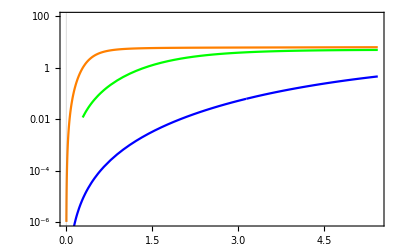

```mathematica
Show[f3,f2,f1]
```

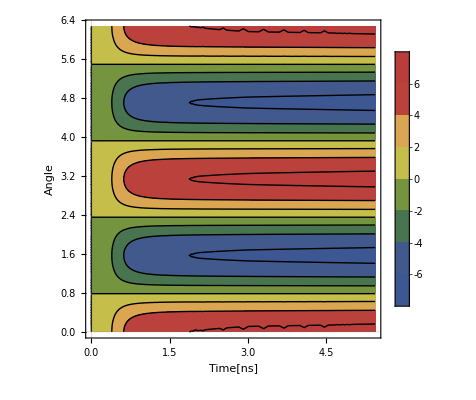

```mathematica
figcontour=ContourPlot[Re[SNR[t,χ,κ,n,ϕ]],{t,0,tmin1},{ϕ,0,2π},LabelStyle->{FontFamily->"Times New Roman",FontSize->18,Black},Frame->True,FrameStyle->{{AbsoluteThickness[2],AbsoluteThickness[2]},{AbsoluteThickness[2],AbsoluteThickness[2]}},PlotTheme->"Scientific",PlotLegends->Automatic,FrameLabel->{"Time[ns]","Angle"},ColorFunction->"DarkRainbow"]
```

```mathematica
Export["C:\\Users\\Mo Zhou\\python file\\paint\\countour.pdf",figcontour];
```